```mathematica
F[s_]:=Module[{p={{0,0}},x=0,y=0,ls=Length[s]},
For[i=1,i≤ls,i++,
If[s[[i]]==0,x+=1];
If[s[[i]]==1,y+=1];
If[s[[i]]==2,x-=1];
If[s[[i]]==3,y-=1];
AppendTo[p,{x,y}];
];
Return[p]]
```

```mathematica
G[s_]:=Module[{p={{0,0,0}},x=0,y=0,z=0,ls=Length[s]},
For[i=1,i≤ls,i++,
If[s[[i]]==0,x+=1];
If[s[[i]]==1,y+=1];
If[s[[i]]==2,z+=1];
If[s[[i]]==3,x-=1];
If[s[[i]]==4,y-=1];
If[s[[i]]==5,z-=1];
AppendTo[p,{x,y,z}];
];
Return[p]]
```

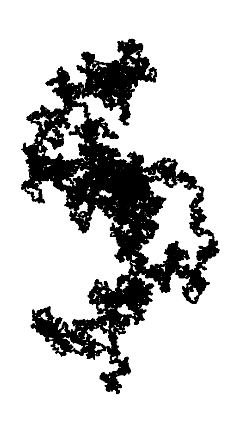

```mathematica
Graphics[Line[F[RealDigits[π,4,100000][[1]]]]]
```

```mathematica
Graphics3D[Line[G[RealDigits[E,6,10000][[1]]]]]
```

-Graphics3D-

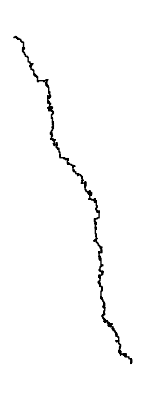

```mathematica
Graphics[Line[F[Mod[ContinuedFraction[π,1000],4]]]]
```

```mathematica
Graphics[Line[F[Mod[ContinuedFraction[E,200],4]]]]
```

-Graphics-